### Bode Plot program for an arbitrary frequency response

#### H (ⅉ ω)=(K ⅉω (ⅉω/z_1+1)...(ⅉω/z_n+1))/(ⅉω (ⅉω/p_1+1)... (ⅉω/p_n+1)) |H(ⅉω)|=20log_10(K)+(∑_(i=1)^n 20 log_10|1+ⅉω/z_i|)-(∑_(j=1)^m 20 log_10|1+ⅉω/p_j|) ϕ(ⅉω)=∑_(i=1)^n arctan(ω/z_i)-∑_(j=1)^m arctan(ω/p_j)

```mathematica
Clear["Global`*"]
K=Input["Enter The Value Of Gain"];
n = Input["Enter The Number Of Poles"];
m=Input["Enter The Number Of Zeroes"];
listOfPoles =Table[Input["Enter The Value Of The nth Pole"],n];
listOfZeros=Table[Input["Enter The Value Of The nth Zero"],m];

(* Processing the zeros in the lists*)
listOfPolesAt0=Select[listOfPoles, #==0 &];
listOfPoles=Select[listOfPoles, #≠0 &];
listOfZerosAt0=Select[listOfZeros, #==0 &];
listOfZeros=Select[listOfZeros, #≠0 &];
```

H(ⅉω)= 20/((1+(ⅈ ω)/8) (1+(ⅈ ω)/5)^2 (1+(ⅈ ω)/3) (1+(ⅈ ω)/2))

H{2,3,5,8} = {19.8608,14.6493,4.19216,-9.41399}

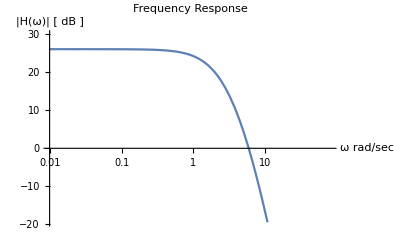

ϕ(ⅉω)= -(180 ArcTan[ω/8])/π-(360 ArcTan[ω/5])/π-(180 ArcTan[ω/3])/π-(180 ArcTan[ω/2])/π

ϕ{2,3,5,8} = {-136.329,-183.793,-249.24,-306.397}

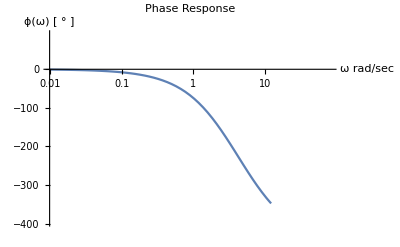

```mathematica
(*Creating the Frequency Response (Magnitude or Transfer Function)*)
H[ω_]:=K*Times@@(1/(1+(ⅉ ω)/#))&[listOfPoles]*Times@@(1+(ⅉ ω)/#)&[listOfZeros] * (ⅉ ω)^Length[listOfZerosAt0]* (1/(ⅉ ω))^Length[listOfPolesAt0];(*This makes the function ∏_(i=1)^n 1/(1+ⅉω/Subscript[p, i]) * ∏_(i=1)^m (1+ⅉω/Subscript[p, i])*)

(*Creating the Phase Response in Degrees*)
phaseZerosAt0 = 90*Length[listOfZerosAt0] ;
phasePolesAt0 = -90*Length[listOfPolesAt0] ;
ϕ[ω_]:=Arg[K]+(Plus@@-(180/π*ArcTan[ω/#]&[listOfPoles]))+(Plus@@(180/π*ArcTan[ω/#]&[listOfZeros]))+phaseZerosAt0+phasePolesAt0 ;

(* These functions join the poles and zeros lists and removes points which would cancel. (e.g. An overlapping pole and zero)*)
numPoints[list_, point_] := Length[Flatten[Position[list, point]]]

(*Actual implimentation of functions from above*)
zerosAndPolesIntersection = listOfZeros∩listOfPoles;
zerosAndPoles = Complement[listOfZeros∪listOfPoles, zerosAndPolesIntersection];
For[i=1, i≤Length[zerosAndPolesIntersection], i++, If[numPoints[listOfZeros, Part[zerosAndPolesIntersection, i]] ≠ numPoints[listOfPoles, Part[zerosAndPolesIntersection, i]], AppendTo[zerosAndPoles, Part[zerosAndPolesIntersection, i]]]]

(* Used for variable plot scaling. Users may wish to change these values.*)
listOfMagnitudesdB=20*Log[10,Abs[H[#]]]&/@zerosAndPoles//N; 
sizeFactor = 0.5;
maxdB=Max[listOfMagnitudesdB];
mindB=Min[listOfMagnitudesdB];
listOfPhases=ϕ[#]&/@zerosAndPoles//N; 
maxPhase=If[Max[listOfPhases]<0,0,Max[listOfPhases]];
minPhase=If[Min[listOfPhases]>0,0,Min[listOfPhases]];

(*Plot Tolarances /  Values*)
lowestωValue=10^-2;
plotMagnitudeTolerances = 10;
plotPhaseTolerances = 90;



(*Evaluates Magnitude (in dB) and Phase at the pole locations*)
listOfPolesEvalPoints = Intersection[zerosAndPoles, listOfPoles];
listOfPolesMagnitudesdB=20*Log[10,Abs[H[#]]]&/@listOfPolesEvalPoints//N; 
listOfPolesPhase=ϕ[#]&/@listOfPolesEvalPoints//N; 

(*Prints and plots (in dB) the Frequency Response*)
StringForm["H(ⅉω)= ``",H[ω]]
StringForm["H`` = ``", listOfPolesEvalPoints,listOfPolesMagnitudesdB]

LogLinearPlot[20*Log[10,Abs[H[ω]]],{ω,lowestωValue,1.5Max[zerosAndPoles]},PlotRange->{{lowestωValue,plotMagnitudeTolerances*Max[zerosAndPoles]},{mindB-plotMagnitudeTolerances,maxdB+plotMagnitudeTolerances}},PlotLabel->"Frequency Response", AxesLabel->{"ω rad/sec","|H(ω)| [ dB ]"},Ticks->{listOfPoles,Automatic}]



(*Prints and plots the Phase Response in Degrees*)
StringForm["ϕ(ⅉω)= ``",ϕ[ω]]
StringForm["ϕ`` = ``", listOfPolesEvalPoints,listOfPolesPhase]
LogLinearPlot[ϕ[ω], {ω,lowestωValue,1.5*Max[zerosAndPoles]},PlotRange->{{lowestωValue,10*Max[zerosAndPoles]},{minPhase - plotPhaseTolerances, maxPhase+plotPhaseTolerances}},PlotLabel->"Phase Response", AxesLabel->{"ω rad/sec","ϕ(ω) [ ° ]"},Ticks->{listOfPoles,Automatic}]
```